# “Statistical Data Analysis on Worldwide Airplane Crashes and Fatalities In Scheduled Passenger flights: Causes, Occurrences and Insights”

## Import Data

```mathematica
(*Set the directory where is located the data*)
directoryPath="C:\\Users\\Camilo Quinceno\\Documents\\MSc Data Sciene\\Semester I\\Introduction to Data Science\\Project\\Dataset";
SetDirectory[directoryPath];
rawData=Import["Aircraft_Incident_Dataset.csv","Data"];
(*Check the dimmension of the imported data*)
Dimensions[rawData]
(*Include other Dataset*)
passengersRawData=Import["API_IS.AIR.PSGR_DS2_en_csv_v2_3852524.csv","Data"];
```

{23520,23}

## Extract Information

```mathematica
(*Extract just the data related with Domestic Scheduled Passenger flies*)
scheduledPassengerRawData = Cases[rawData,{_,_,_,_,a_,_,_,_,_,_,_,_,_,_,_,_,b_,___}/;a=="Domestic Scheduled Passenger" && b==0];
scheduledPassengerRawData//Dimensions
```

{2249,23}

```mathematica
(*Extract just the data related with Domestic Scheduled Passenger flies and fatalities*)
scheduledPassengerRawDataFatalities = Cases[rawData,{_,_,_,_,a_,_,_,_,_,_,_,_,_,_,_,_,b_,___}/;a=="Domestic Scheduled Passenger" && b>0];
scheduledPassengerRawDataFatalities//Dimensions
```

{1755,23}

## Causes

### Determine the most common reason/cause of airplane crashes and their fatality rate?

#### What are the categories of cause most common in accidents with fatalities?

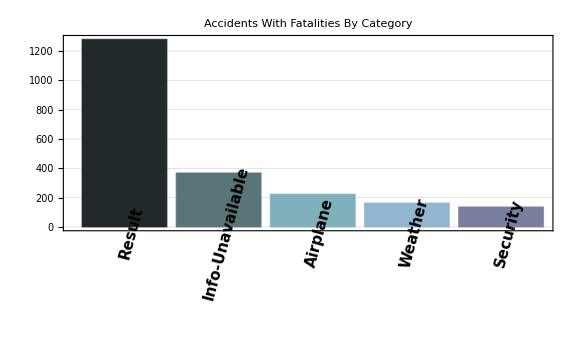

```mathematica
(*Extract just the data related with incident cause (Column 7) when the accidents have fatalities*)
allCausesFatalities=scheduledPassengerRawDataFatalities[[All,7]]//Flatten;
(*Separate each value by "," Character, due to each value has multiple causes, For example: Airplane - Engines,Airplane - Engines - Fire, Cargo - Overloaded  *)
allCausesFatalities=TextWords[StringSplit[#,","]]&/@allCausesFatalities;
(*Iterate each flight to get just the first word of each cause, for example: Airplane - Engines -> Airplane *)
allCausesFatalities=Table[allCausesFatalities[[i]][[j]][[1]],{i,Length[allCausesFatalities]},{j,Length[allCausesFatalities[[i]]]}];
(* Delete the duplicate cases in each flight, for example:  Airplane - Engines,Airplane - Engines - Fire, Cargo - Overloaded -> Airplane, Cargo *)
allCausesFatalities=DeleteDuplicates[#]&/@allCausesFatalities;
(* Delete word mountain due to it is not a category and flatten all the categories to count them *)
causesCartegoryFatalityAssociation=Sort[KeyDrop[allCausesFatalities//Flatten//Counts,{"mountain","forced"}],Greater][[;;5]];
BarChart[causesCartegoryFatalityAssociation,PlotLabel->"Accidents With Fatalities By Category",ChartLabels->Placed[Keys[causesCartegoryFatalityAssociation],Below,Rotate[#,Pi/2.4]&],PlotTheme->"Detailed",ChartStyle->"AtlanticColors",ImageSize->Large,LabelStyle->Directive[Bold, 15]]
```

#### What happen with these categories in accidents without fatalities?

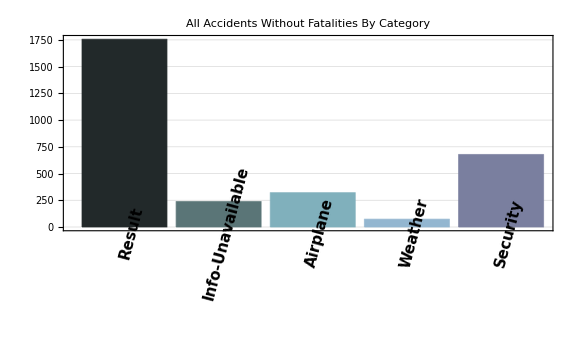

```mathematica
allCauses=scheduledPassengerRawData[[All,7]]//Flatten;
(*Separate each value by "," Character, due to each value has multiple causes, For example: Airplane - Engines,Airplane - Engines - Fire, Cargo - Overloaded  *)
allCauses=TextWords[StringSplit[#,","]]&/@allCauses;
(*Iterate each flight to get just the first word of each cause, for example: Airplane - Engines -> Airplane *)
allCauses=Table[allCauses[[i]][[j]][[1]],{i,Length[allCauses]},{j,Length[allCauses[[i]]]}];
(* Delete the duplicate cases in each flight, for example:  Airplane - Engines,Airplane - Engines - Fire, Cargo - Overloaded -> Airplane, Cargo *)
allCauses=DeleteDuplicates[#]&/@allCauses;
(* Delete word mountain due to it is not a category and flatten all the categories to count them *)
causesCartegoryAssociation=KeyDrop[allCauses//Flatten//Counts,{"mountain","forced"}];
causesCartegoryAssociation= {causesCartegoryAssociation["Result"],causesCartegoryAssociation["Info-Unavailable"],causesCartegoryAssociation["Airplane"],causesCartegoryAssociation["Weather"],causesCartegoryAssociation["Security"]};
BarChart[causesCartegoryAssociation,ChartLabels->Placed[Keys[causesCartegoryFatalityAssociation],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"All Accidents Without Fatalities By Category",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 15]]
```

```mathematica
keys=Style[#,12]&/@Keys[causesCartegoryFatalityAssociation];
```

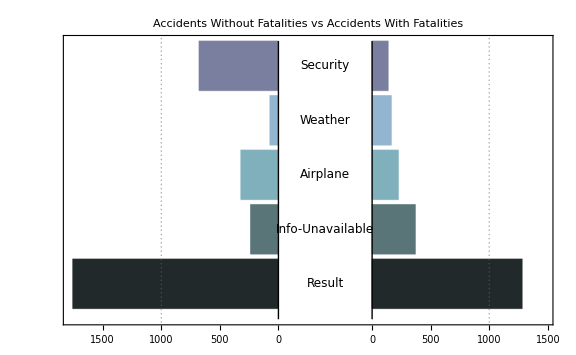

```mathematica
PairedBarChart[causesCartegoryAssociation,causesCartegoryFatalityAssociation,ChartLabels->keys,ChartStyle->"AtlanticColors",PlotLabel->Style["Accidents Without Fatalities vs Accidents With Fatalities",20],BarSpacing->{800,0,0.1},PlotTheme->"Detailed",ImageSize->Large]
```

#### What is the subcategories inside “Result” most common in accidents without fatalities?

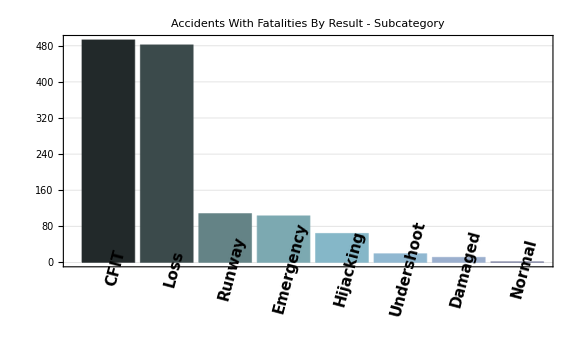

```mathematica
(*Extract the column with causes (Column 7) *)
subCategories=scheduledPassengerRawDataFatalities[[All,7]]//Flatten;
(*Divide the values of the column 7 by the string ","*)
subCategories=TextWords[StringSplit[#,","]]&/@subCategories;
(*Get just the elements that contains the word "Result" ","*)
subCategories=Table[Cases[subCategories[[i]],{a_,___} /; a=="Result"],{i,Length[subCategories]}];
(* Get the element after the word result, for example: {Result,Runway excursion} -> Runway  *)
subCategories=Table[subCategories[[i]][[j]][[2]],{i,Length[subCategories]},{j,Length[subCategories[[i]]]}];
(* Delete duplicate cases per row *)
subCategories=DeleteDuplicates[#]&/@subCategories;
(* Flatten and count all the elements *)
subCategoriesFatalities=subCategories//Flatten//Counts;
BarChart[Sort[subCategoriesFatalities,Greater],ChartLabels->Placed[Keys[Sort[subCategoriesFatalities,Greater]],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents With Fatalities By Result - Subcategory",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 15]]
```

#### What is the subcategories inside “Result” most common in accidents ?

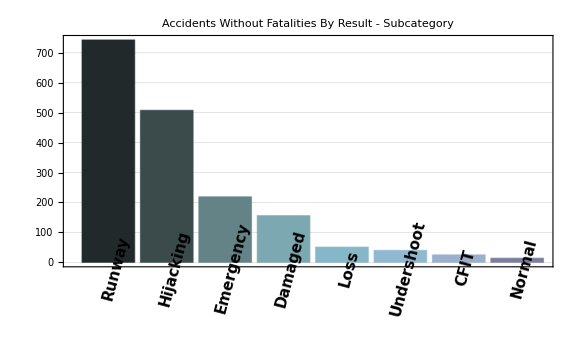

```mathematica
(*Extract the column with causes (Column 7) *)
subCategories=scheduledPassengerRawData[[All,7]]//Flatten;
(*Divide the values of the column 7 by the string ","*)
subCategories=TextWords[StringSplit[#,","]]&/@subCategories;
(*Get just the elements that contains the word "Result" ","*)
subCategories=Table[Cases[subCategories[[i]],{a_,___} /; a=="Result"],{i,Length[subCategories]}];
(* Get the element after the word result, for example: {Result,Runway excursion} -> Runway  *)
subCategories=Table[subCategories[[i]][[j]][[2]],{i,Length[subCategories]},{j,Length[subCategories[[i]]]}];
(* Delete duplicate cases per row *)
subCategories=DeleteDuplicates[#]&/@subCategories;
(* Flatten and count all the elements *)
subCategories=subCategories//Flatten//Counts;
BarChart[Sort[subCategories,Greater],ChartLabels->Placed[Keys[Sort[subCategories,Greater]],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents Without Fatalities By Result - Subcategory",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 15]]
```

```mathematica
keys=Style[#,12]&/@Keys[KeySort[subCategories]];
```

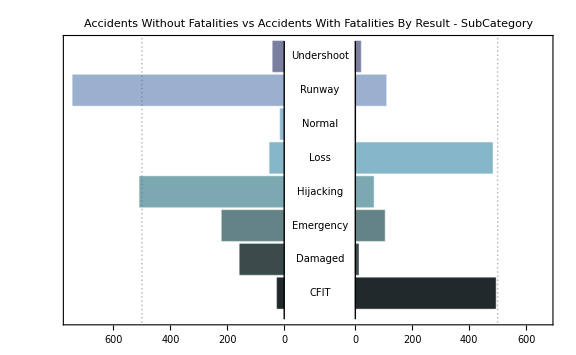

```mathematica
PairedBarChart[subCategories//KeySort,subCategoriesFatalities//KeySort,ChartLabels->keys,ChartStyle->"AtlanticColors",PlotLabel->Style["Accidents Without Fatalities vs Accidents With Fatalities By Result - SubCategory",15],BarSpacing->{250,0,0.1},PlotTheme->"Detailed",ImageSize->Large]
```

## Ocurrences

### Determine what airlines/brand have most commonly been involved in accidents and over what geographical regions?

#### What is the brand involved in more accidents without accidents?

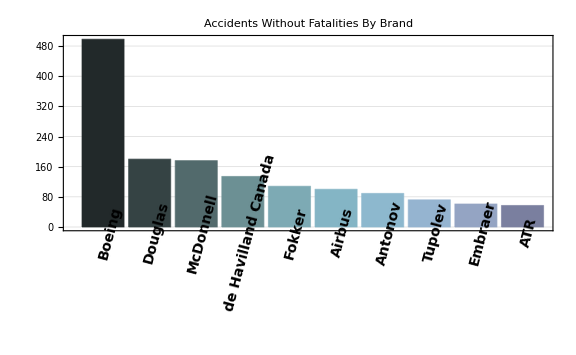

```mathematica
(*Extract the values of the column 2 (Aircraft models)*)
aircraftModels=Table[scheduledPassengerRawData[[i]][[2]],{i,Length[scheduledPassengerRawData]}];
 (*Split the string in the coloumn to select just the first word of the aircraft model, the first word is the brand of the model) and count how many times appears each brand in the column*)
associationBrandCount =Sort[StringSplit[#][[1]]&/@aircraftModels//Counts,Greater];
aircratBrands = associationBrandCount//Keys;
accidentsByBrand=associationBrandCount//Values;
 (*Plot the Top 10 brands that are involved in accidents*)
BarChart[accidentsByBrand[[;;10]],ChartLabels->Placed[aircratBrands[[;;10]]/."de"-> "de Havilland Canada",Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents Without Fatalities By Brand",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 14]]
```

#### What is the brand involved in more accidents (withFatalities)?

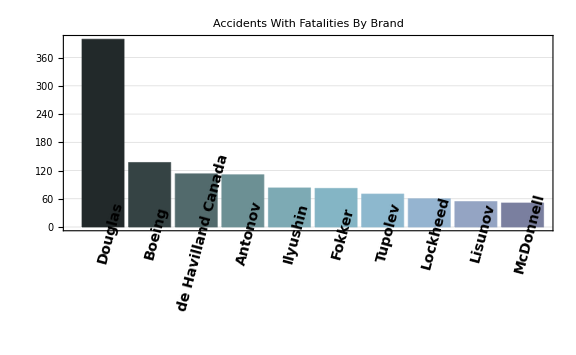

```mathematica
(*Extract the values of the column 2 (Aircraft models)*)
aircraftModelsFatalities=Table[scheduledPassengerRawDataFatalities[[i]][[2]],{i,Length[scheduledPassengerRawDataFatalities]}];
 (*Split the string in the coloumn to select just the first word of the aircraft model, the first word is the brand of the model) and count how many times appears each brand in the column*)
associationBrandCountFatalities =Sort[StringSplit[#][[1]]&/@aircraftModelsFatalities//Counts,Greater];
 (*Separate brands and the number of times that each brand appears in the column to plot the information in a barchart*)
aircratBrandsFatalities = associationBrandCountFatalities//Keys;
accidentsByBrandFatalities=associationBrandCountFatalities//Values;
 (*Plot the Top 10 brands that are involved in accidents with fatalities*)
BarChart[accidentsByBrandFatalities[[;;10]],ChartLabels->Placed[aircratBrandsFatalities[[;;10]]/."de"-> "de Havilland Canada",Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents With Fatalities By Brand",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 14]]
```

#### What is the Airline involved in more accidents (withFatalities)?

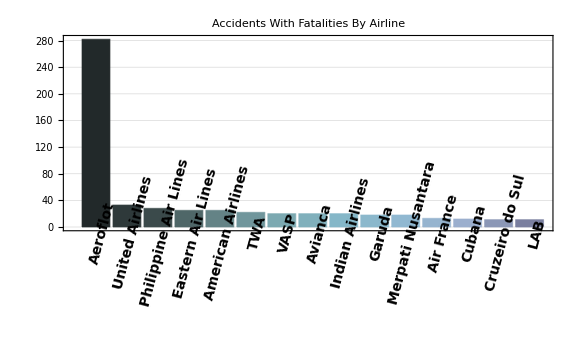

```mathematica
(*Extract the values of the column 4 (Aircraft_Operator)*)
aircraftOperators=Table[scheduledPassengerRawDataFatalities[[i]][[4]],{i,Length[scheduledPassengerRawDataFatalities]}];
(*Combine all Aeroplot variants, For instance: Aeroflot Moscow -> Aeroflot *)
aircraftOperators =StringReplace[#,"Aeroflot"~~__->"Aeroflot"]&/@aircraftOperators;
(*Remove all op.for and get just the aeroline in charge, For instance: AeroPerlas op.for SANSA -> SANSA*)
aircraftOperators=StringReplace[#,__~~"op.for"~~__->StringSplit[#,"op.for"][[-1]]]&/@aircraftOperators;
aircraftOperators=StringReplace[#,__~~"opf"~~__->StringSplit[#,"opf"][[-1]]]&/@aircraftOperators;
aircraftOperators=StringReplace[#,__~~"opb"~~__->StringSplit[#,"opb"][[-1]]]&/@aircraftOperators;
(*Extract just the words of each element to eliminate whitespace, for instance: "  Air France", "Air France  "*)
aircraftOperatorsSepatared = TextWords/@aircraftOperators;
(*Add just one whitespace between words*)
aircraftSeparatedBlancked = Table[Riffle[aircraftOperatorsSepatared[[i]]," "],{i,Length[aircraftOperatorsSepatared]}];
(*Join each element with just one whitespace*)
aircraftUnited=StringJoin/@aircraftSeparatedBlancked;
(*Count how many times each Airline appear*)
aircraftAssosiation=Sort[aircraftUnited//Counts,Greater];
BarChart[aircraftAssosiation[[;;15]],ChartLabels->Placed[Keys[aircraftAssosiation[[;;15]]],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents With Fatalities By Airline",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 14]]
```

#### What is the Airline involved in more accidents without Fatalities?

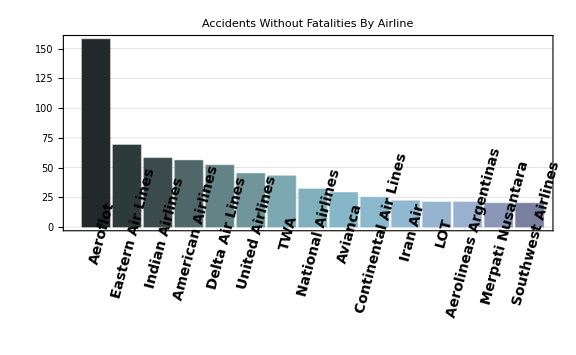

```mathematica
(*Extract the values of the column 4 (Aircraft_Operator)*)
aircraftOperators2=Table[scheduledPassengerRawData[[i]][[4]],{i,Length[scheduledPassengerRawData]}];
(*Combine all Aeroplot variants, For instance: Aeroflot Moscow -> Aeroflot *)
aircraftOperators2 =StringReplace[#,"Aeroflot"~~__->"Aeroflot"]&/@aircraftOperators2;
(*Remove all op.for and get just the aeroline in charge, For instance: AeroPerlas op.for SANSA -> SANSA*)
aircraftOperators2=StringReplace[#,__~~"op.for"~~__->StringSplit[#,"op.for"][[-1]]]&/@aircraftOperators2;
aircraftOperators2=StringReplace[#,__~~"opf"~~__->StringSplit[#,"opf"][[-1]]]&/@aircraftOperators2;
aircraftOperators2=StringReplace[#,__~~"opb"~~__->StringSplit[#,"opb"][[-1]]]&/@aircraftOperators2;
(*Extract just the words of each element to eliminate whitespace, for instance: "  Air France", "Air France  "*)
aircraftOperatorsSepatared2 = TextWords/@aircraftOperators2;
(*Add just one whitespace between words*)
aircraftSeparatedBlancked2 = Table[Riffle[aircraftOperatorsSepatared2[[i]]," "],{i,Length[aircraftOperatorsSepatared2]}];
(*Join each element with just one whitespace*)
aircraftUnited2=StringJoin/@aircraftSeparatedBlancked2;
(*Count how many times each Airline appear*)
aircraftAssosiation2=Sort[aircraftUnited2//Counts,Greater];
BarChart[aircraftAssosiation2[[;;15]],ChartLabels->Placed[Keys[aircraftAssosiation2[[;;15]]],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents Without Fatalities By Airline",PlotTheme->"Detailed",ImageSize->Large,LabelStyle->Directive[Bold, 14]]
```

### Where is the most dangerous place to take a fly (withFatalities)?

```mathematica
(*Extract the information in the column 20 (Departure Airport)*)
airports=Table[scheduledPassengerRawDataFatalities[[i]][[20]],{i,Length[scheduledPassengerRawDataFatalities]}];
(*Extract the last word of the data in the column, the last word is the country where the plane start the travel*)
countries= Table[StringSplit[#,","][[-1]]&/@airports,{i,Length[airports]}];
(*Eliminate the cases where the country is unknown("?")*)
countriesSeparated = TextWords/@Cases[countries[[1]],a_/;a!="?"];
(*In the columns are countries that are the same but they are write with different spaces, so we select just the words, after that we add an space between the words to rebuild each country*)
countriesSeparatedBlancked = Table[Riffle[countriesSeparated[[i]]," "],{i,Length[countriesSeparated]}];
countriesAssosiation=StringJoin/@countriesSeparatedBlancked;
(*Convert each country to an entity, eliminate the placese that are not recognized by wolfram as a country and then count how many times appear each country*)
contriesEntityAssociation=Sort[DeleteCases[Interpreter["Country"][#]&/@countriesAssosiation,_Failure]//Counts,Greater];
GeoRegionValuePlot[contriesEntityAssociation,ImageSize->Large]
```

-Graphics-

## Insights

#### Determine if air transportation has become safer over time

#### Determine if air transportation has become safer over time (Fatalities by year)?

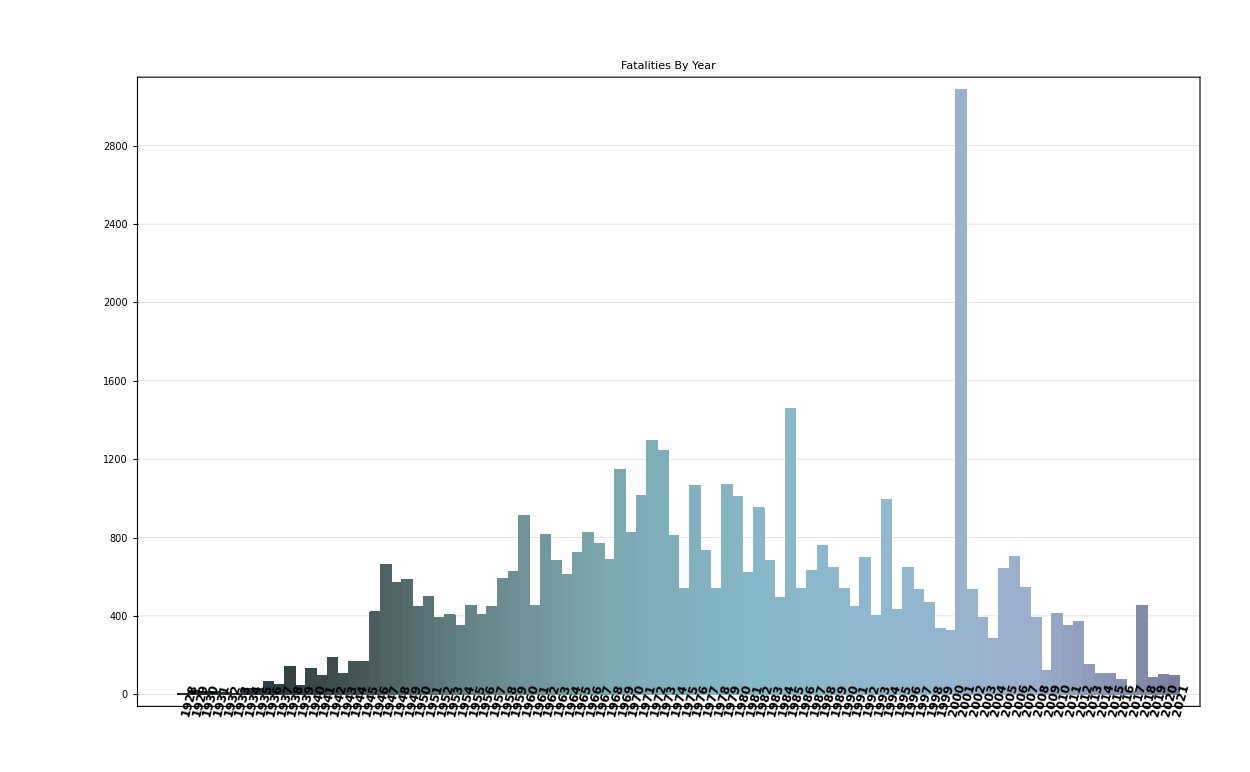

```mathematica
domesticScheduledPassengerDateDataFatalities=scheduledPassengerRawDataFatalities;
(*Convert the column 1 in a format that DateObject can recognize{Year,Month,day}*)
Table[domesticScheduledPassengerDateDataFatalities[[i]][[1]]=StringSplit[domesticScheduledPassengerDateDataFatalities[[i]][[1]],"-"]/.{a_,b_,c_}:> {ToExpression[c],b,ToExpression[a]}/.{"JAN"->1,"FEB"->2,"MAR"->3,"APR"->4,"MAY"->5,"JUN"->6,"JUL"->7,"AUG"->8,"SEP"->9,"OCT"->10,"NOV"->11,"DEC"->12},{i,Length[domesticScheduledPassengerDateDataFatalities]}];
(*Convert in a DataObject each element of the column 1*)
Table[domesticScheduledPassengerDateDataFatalities[[i]][[1]]= DateObject[domesticScheduledPassengerDateDataFatalities[[i]][[1]]],{i,Length[domesticScheduledPassengerDateDataFatalities]}];
(*Extract the information of the column 1 and 17 (Date,Fatalities)*)
fatalitiesbyDate=domesticScheduledPassengerDateDataFatalities[[All,{1,17}]]//Reverse;
(*Create the association Year->Number of fatalites)*)
fatalitiesbyDateAssociation=Merge[fatalitiesbyDate/.{a_,b_}:><|a["Year"]->b|>,Total];
(*Plot the number of fatalites by year*)
BarChart[fatalitiesbyDateAssociation,ChartLabels->Placed[Keys[fatalitiesbyDateAssociation],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Fatalities By Year",PlotTheme->"Detailed",ImageSize->1250,LabelStyle->Directive[Bold, 12]]
```

#### Determine if air transportation has become safer over time (Accidents by year)?

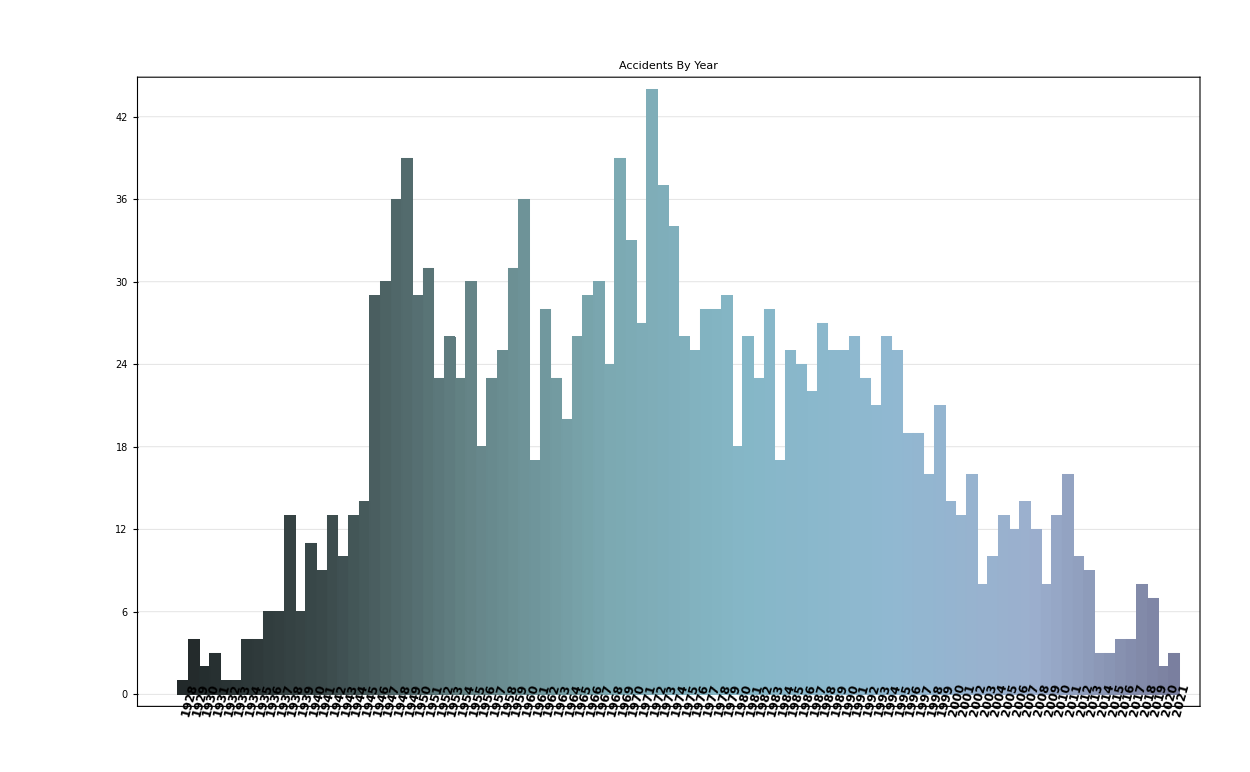

```mathematica
(*Count how many accidents happen by year*)
AccidentsbyYear=fatalitiesbyDate/.{a_,b_}:>a["Year"]//Counts;
BarChart[AccidentsbyYear,ChartLabels->Placed[Keys[AccidentsbyYear],Below,Rotate[#,Pi/2.4]&],ChartStyle-> "AtlanticColors",PlotLabel->"Accidents By Year",PlotTheme->"Detailed",ImageSize->1250,LabelStyle->Directive[Bold, 12]]
```

```mathematica
passengersData=Transpose[passengersRawData[[5;;,11;;65]]];
passengersData=Table[passengersData[[i]][[1]]->Total[DeleteCases[passengersData[[i]][[2;;]],""]],{i,Length[passengersData]}];
passengersData=Sort[Append[passengersData,Append[Table[i->0,{i,1928,1965}],2021->0]]]//Flatten//Values;
accidentByYearList=Values[AccidentsbyYear];
fatalitiesbyDateAssociationList = Values[fatalitiesbyDateAssociation];
```

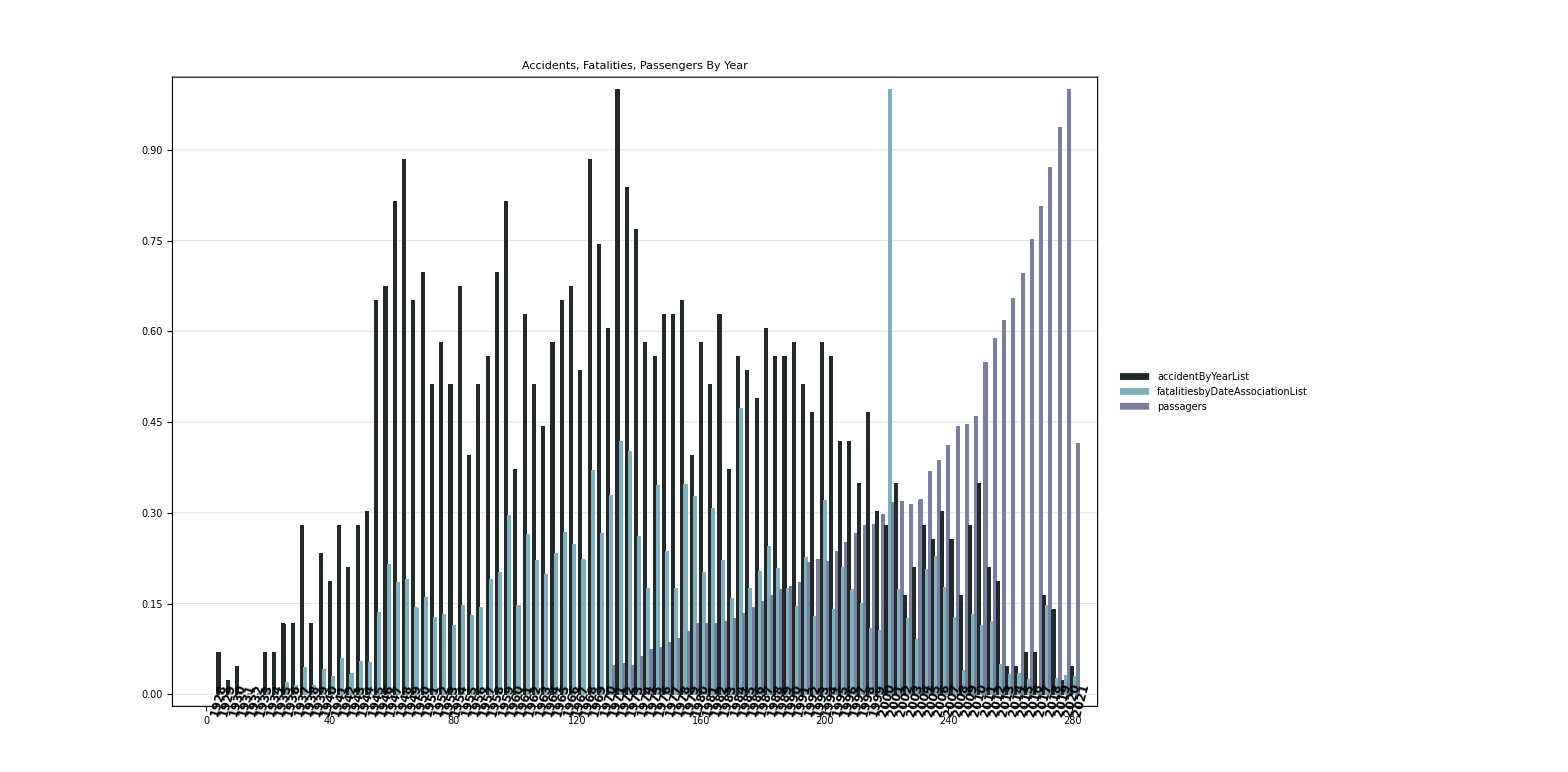

```mathematica
BarChart[Transpose[{Rescale[accidentByYearList]//N,Rescale[fatalitiesbyDateAssociationList]//N,Rescale[passengersData]//N}],ChartLegends->{"accidentByYearList","fatalitiesbyDateAssociationList","passagers"},ChartLabels->{Placed[Keys[fatalitiesbyDateAssociation],Below,Rotate[#,Pi/2.4]&],None},ChartStyle-> "AtlanticColors",PlotLabel->"Accidents, Fatalities, Passengers By Year",PlotTheme->"Detailed",ImageSize->1250,LabelStyle->Directive[Bold, 12]]
```